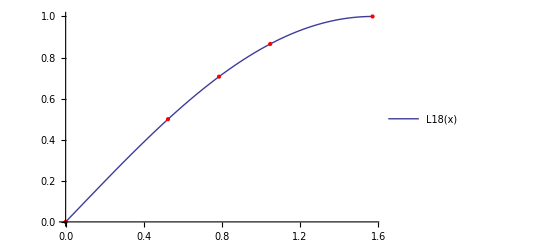

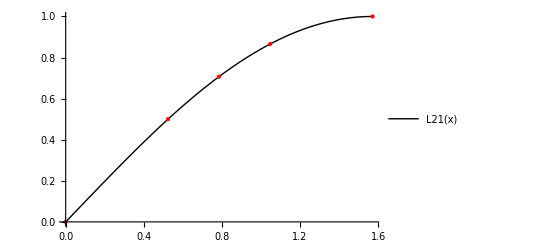

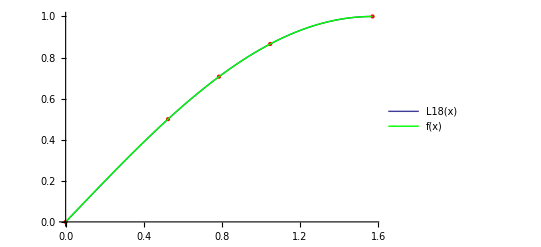

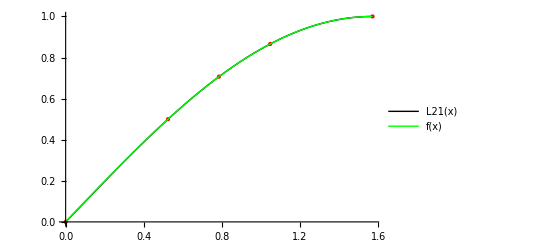

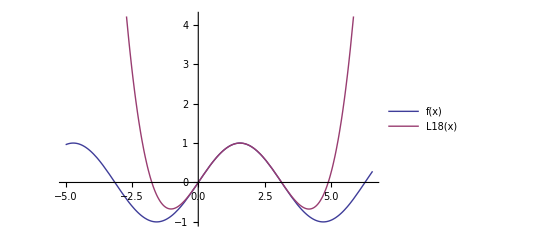

```mathematica
(*Построим данную таблично-заданную функцию*)
X={0.000,0.524,0.785,1.047,1.571};
Y={0.000,0.500,0.707,0.866,1.000};
(*Определим степень многочлена Лагранжа*)
n=Dimensions[X][[1]]-1;
(*Построим многочлен Лагранжа методами XVIII века*)L18[x_]=Sum[Y[[i]]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,1,i-1}]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,i+1,n+1}],{i,1,n+1}];
(*Построим многочлен Лагранжа методами XXI века*)
(*Построим матрицу Вандермонда*)
W=Table[1,{i,1,n+1},{j,1,n+1}];
For[i=1,i≤n+1,i++,
For[j=2,j≤n+1,j++,
W[[i,j]]=X[[i]]^(j-1)
]
];
(*Найдем коэффициенты многочлена Лагранжа*)
A=Inverse[W].Y;
(*Построим многочлен Лагранжа*)
L21[x_]=Sum[A[[j]]*x^(j-1),{j,1,n+1}];
(*Построим график многочлена Лагранжа и таблично-заданной функции в одной системе координат*)
G18=Plot[L18[x],{x,X[[1]],X[[n+1]]},PlotLegends->"Expressions"];
G21=Plot[L21[x],{x,X[[1]],X[[n+1]]},PlotStyle->Black,PlotLegends->"Expressions"];
F=Table[{X[[j]],Y[[j]]},{j,1,n+1}];
GT=ListPlot[F,PlotStyle->Red,PlotLegends->"F"];
Show[G18,GT]
Show[G21,GT]
(*Зададим приближаемую функцию*)
f[x_]=Sin[x];
G=Plot[f[x],{x,X[[1]],X[[n+1]]},PlotStyle->Green,PlotLegends->"Expressions"];
Show[G18,GT,G]
Show[G21,GT,G]
(*Построим график прближаемой функции и многочлена Лагранжа вне отрезка интерполяции*)GOut=Plot[{f[x],L18[x]},{x,X[[1]]-5,X[[n+1]]+5},PlotLegends->"Expressions"]
```